```mathematica
f1=InterpolatingPolynomial[{{1/2 (1-Sqrt[3/5]),1},{1/2,0},{1/2 (1+Sqrt[3/5]),0}},x];
f2=InterpolatingPolynomial[{{1/2 (1-Sqrt[3/5]),0},{1/2,1},{1/2 (1+Sqrt[3/5]),0}},x];
f3=InterpolatingPolynomial[{{1/2 (1-Sqrt[3/5]),0},{1/2,0},{1/2 (1+Sqrt[3/5]),1}},x];
```

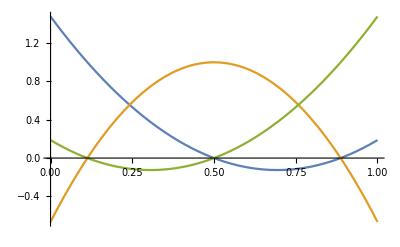

```mathematica
Plot[{f1,f2,f3},{x,0,1}]
```

```mathematica
ML={{Integrate[f1,{x,-2,-1}],Integrate[f2,{x,-2,-1}],Integrate[f3,{x,-2,-1}]},
{Integrate[f1,{x,-1,0}],Integrate[f2,{x,-1,0}],Integrate[f3,{x,-1,0}]},
{Integrate[f1,{x,0,1}],Integrate[f2,{x,0,1}],Integrate[f3,{x,0,1}]}};
MC={{Integrate[f1,{x,-1,0}],Integrate[f2,{x,-1,0}],Integrate[f3,{x,-1,0}]},
{Integrate[f1,{x,0,1}],Integrate[f2,{x,0,1}],Integrate[f3,{x,0,1}]},
{Integrate[f1,{x,1,2}],Integrate[f2,{x,1,2}],Integrate[f3,{x,1,2}]}};
MR={{Integrate[f1,{x,0,1}],Integrate[f2,{x,0,1}],Integrate[f3,{x,0,1}]},
{Integrate[f1,{x,1,2}],Integrate[f2,{x,1,2}],Integrate[f3,{x,1,2}]},
{Integrate[f1,{x,2,3}],Integrate[f2,{x,2,3}],Integrate[f3,{x,2,3}]}};
```

```mathematica
Simplify[ML]
Simplify[MC]
Simplify[MR]
```

{{245/18+2 √(5/3),-236/9,245/18-2 √(5/3)},{65/18+√(5/3),-56/9,65/18-√(5/3)},{5/18,4/9,5/18}}

{{65/18+√(5/3),-56/9,65/18-√(5/3)},{5/18,4/9,5/18},{65/18-√(5/3),-56/9,65/18+√(5/3)}}

{{5/18,4/9,5/18},{65/18-√(5/3),-56/9,65/18+√(5/3)},{245/18-2 √(5/3),-236/9,245/18+2 √(5/3)}}

```mathematica
InvML=Simplify[Inverse[ML]]
InvMC=Simplify[Inverse[MC]]
InvMR=Simplify[Inverse[MR]]
```

{{1/60 (2-3 √15),-1/15+√(3/5),1/60 (62-9 √15)},{-1/24,1/12,23/24},{1/60 (2+3 √15),-1/15-√(3/5),1/60 (62+9 √15)}}

{{1/60 (2+3 √15),14/15,1/60 (2-3 √15)},{-1/24,13/12,-1/24},{1/60 (2-3 √15),14/15,1/60 (2+3 √15)}}

{{1/60 (62+9 √15),-1/15-√(3/5),1/60 (2+3 √15)},{23/24,1/12,-1/24},{1/60 (62-9 √15),-1/15+√(3/5),1/60 (2-3 √15)}}